# Generating the Perfect Scrabble Game

### Introduction

In December of 2023, a video was uploaded to YouTube by Scrabble Grandmaster (GM) Mack Meller. The video can be found at this link. Mack is the winner of the 2024 North American Scrabble Championships, and uploads videos almost every day of his games against the strongest Scrabble bots, or other GMs. 

I have played Scrabble with family ever since I can remember, and began playing online around 2 years ago. This video sparked a whole new interest in Scrabble for me.

### Terminology

I will start by defining some terminology, and I will assume that you know the basics of how to play Scrabble because you chose to read this post!

Bingo - A player uses all seven tiles on their rack in a single turn, receiving a 50-point bonus.
Blank - A blank tile can represent any letter, and scores zero points.
Overlap - A word is formed using a tile already on the board from a previous turn.
Hook - A word is played that places a letter onto the start or end of a word. For example: (S)TRAINER, TRAINER(S). The letter “S” has ‘hooked’ onto the word “TRAINER”.
Tile Bag - The distribution of exactly 100 tiles corresponding to letters in the English Alphabet, or blanks. There are 9 As, 2 Bs, 2 Cs, 4 Ds, 12 Es, 2 Fs, 3 Gs, 2 Hs, 9 Is, 1 J, 1 K, 4 Ls, 2 Ms, 6 Ns, 8 Os, 2 Ps, 1 Q, 6 Rs, 4 Ss, 6 Ts, 4 Us, 2 Vs, 2 Ws, 1 X, 2 Ys, 1 Z, and 2 Blanks (usually represented by the “?” symbol).

### The Perfect Game

In the video, Mack takes us turn-by-turn through a fictional—but technically possible—Scrabble game between two players.
The game belongs to a specific set of all possible Scrabble games because of some interesting constraints:

Every turn, for both players, must be a Bingo.

Score as many points as possible.

It must end in a tie.

I became fascinated by the difficulty in satisfying even the first of these constraints, let alone all three.

So let’s see what a game like this would entail:
Player A goes first with a 7-letter Bingo. 
Player B must play 7 letters too, either making use of an overlap through Player A’s turn to make an 8-letter word, or play a 7-letter word using an available Hook. 
This continues back and forth, until each player has had seven turns—fourteen in total—and a total of 14 x 7 = 98 tiles exist on the Scrabble board.
Since Player B has the even-numbered turns, Player B has the final turn and Player A is left with two tiles (100 - 98 = 2). In competitive Scrabble, twice the total value of these two tiles is added to Player B’s final score.

### The Scrabble-gorithm

My goal was to algorithmically generate the fourteen valid Bingos, using only the tiles available in the Tile Bag. My plan during this project was to define some checkpoints that constituted a successful ‘version’ of the problem:

Version 1: Generate fourteen 7-letter Bingos, with no overlaps, using only the tiles available in the Tile Bag.

Version 2: Generate a starting 7-letter Bingo followed by thirteen 8-letter Bingos, each of which overlap a single tile from exactly one Bingo that has already been played, and using only the tiles available in the Tile Bag.

Version 3: The same as Version 2, but ensure the words fit on a standard 15x15 Scrabble board.

### Version 1: 7 Letter Scrabble-gorithm

It is important to note that I did not start working on any visualizations on a “real” Scrabble Board until Version 3 was almost complete. This challenge began as simply a computational word game; I wanted to solve a word problem much faster than a human ever could. 

Starting this as a human, we almost have too clean a slate. Where do you start? Perhaps you think of nine or ten Bingos, making sure you avoid words like “SUCCESS” which blasts through both of your available Cs and 75% of your Ss. Inevitably, you reach a tile pool that looks bleak. You cannot seem to make out any possible 7-letter words, and perhaps even your precious vowel supply is running low, or too high!

My program has perfect word knowledge, thanks to a complete dictionary I imported.

```mathematica
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
```

I began by scrambling the dictionary randomly, and grouping the words according to their length. Remember we are only concerned with 7-letter words in this Version. The crucial requirement of this algorithm is to keep track of the tiles you have remaining, so at the beginning of every iteration I defined remainingCounts to be an association of tile → quantity key-value pairs. You can see that this matches the Tile Bag I defined in the terminology.

```mathematica
remainingCounts=tiles[[All,"Quantity"]]
```

<|A→9,B→2,C→2,D→4,E→12,F→2,G→3,H→2,I→9,J→1,K→1,L→4,M→2,N→6,O→8,P→2,Q→1,R→6,S→4,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2|>

I iterated through the scrambled list of 7-letter words and performed a check with each new word that it was constructable with the tiles specified in remainingCounts, ensuring this was updated after each constructable word. Unconstructable words that caused one or more values in remainingCounts to become negative were discarded, and the iteration continues until the list ends. For example, a word like “KINFOLK” would be refused from the jump due to their being only 1 K in the Tile Bag. 
The image below shows the algorithm in action for the first few Bingos.

-Graphics-

The stochastic nature of this process sometimes leads one to a point where, even with 21 letters remaining, a valid 7-letter word cannot be constructed.

	-Graphics-

I can perform a check just to be sure.

```mathematica
Select[wordsByLength[7],SubsetQ[Tally[Characters[#]],Tally[Characters["AAAAEFFGGIIIIJOOQVVXY"]]]&]
```

{}

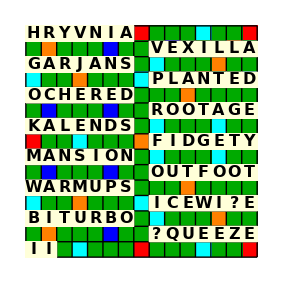
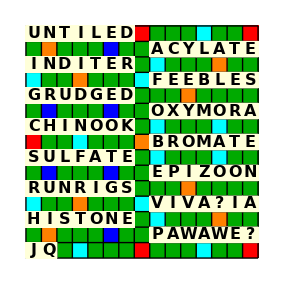
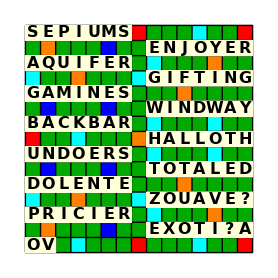
But what about blanks? I hear you cry. Allowing for the use of a blank tile here would certainly enable many valid words to be played, but remember there are three turns left! Casual Blank usage early on will almost certainly leave us stuck with nine letters on turn fourteen, out of which it would be impossible to make a Bingo. This is where I make the decision to allow for the use of exactly one blank on turn thirteen, and exactly one blank on turn fourteen, giving us the degree of freedom when we need it most.
From a functionality perspective, this is as simple as allowing that exactly one key (letter) in remainingCounts may temporarily take on the value of -1 when remainingCounts is updated. This key (letter) is designated as the blank for that turn, then its value is set to zero.

Here, we were only one Bingo away from a successful iteration. By carefully examining the “Tiles Left”, one can see that the algorithm has employed a blank as a “B” to form the word “PAXIUBA” (a type of Brazilian palm tree) on turn thirteen. Unfortunately, even allowing the use of a blank on the final turn, there are no valid Bingos that can be made from the remaining nine tiles.

-Graphics-

And so, all that is left is run this algorithm until we achieve fourteen Bingos. 
I began uploading to a database in the Wolfram Cloud whenever I had a successful iteration, such that I can choose some cool examples to share. Furthermore, I kept track of the leftover tiles, and the letters employed as blanks.

-Graphics-

Here is a visualization on a Scrabble Board of some more examples. Bingos one to seven are on the left side from top to bottom, and Bingos eight to fourteen are on the right. The two leftover tiles are in the lower left corner, and the blanks are indicated by “?”. 
 I find it fascinating to see which unusual Bingos to which the algorithm has resorted for the later turns as a result of the strange mix of tiles remaining. Also, notice how the relative consonant/vowel-heaviness of the available pool of tiles in turns thirteen and fourteen affects the Bingos that are selected.

Version 1 was complete.
-Graphics--Graphics--Graphics-

### Version 2: 8-Letter Scrabble-gorithm

Most of the hard work for this Version had already been completed. I just needed a way of choosing the overlapping tile. The overlapping tile must be a member of the intersection of characters in the new word, and characters in previous Bingos.
The variable usedCounts is an association similar to remainingCounts, except it tracks the tiles used rather than the tiles remaining. In this example, it assumes the word “SCIENCE” was played first, and we are checking the overlap tile options for the word “TUNGSTEN”.

```mathematica
usedCounts=Sort[Counts[Characters["SCIENCE"]]];
word="TUNGSTEN";
overlapOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]
```

{E,N,S}

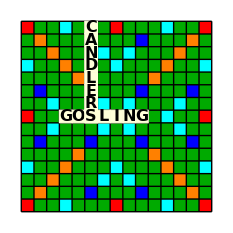
If this intersection is empty, the word is rejected and a new word is selected. 
The following is an example of that exact situation, which provokes a new selection of the Bingo to be played in the second turn. It is worth mentioning that “QUIZZIFY” would also be rejected on the basis of having 2 Zs, however this check comes later. 
Perceptive readers might envisage the word “QUIZZIFY” perhaps being valid in turns thirteen and fourteen, provided that Z can be the overlap tile, and a blank is employed as the other Z. Fantastic!

-Graphics-

Also, the overlap tile must not be double-counted when updating the remaining tiles.

-Graphics-

Notice how there is only one S in the “Tiles Used” because I have accounted for the fact it is the overlap tile, and would only appear once ‘on the board’. 
-Graphics-

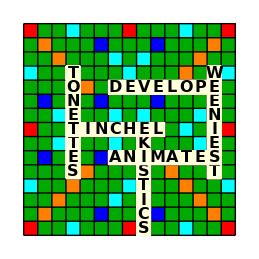
It is worth mentioning again that this visualization is merely to aid the reader’s understanding. This Version does not ‘care’ about board position—or actually being a valid Scrabble play. The only thing that matters is that we select words composed of tiles that remain within the constraints of the Tile Bag. 
What would this correspond to physically? I suppose it would mean that the Scrabble Board can be infinitely large, or perhaps that you are permitted to stack tiles on top of already played tiles (normal to the plane of the board).

So lets assume that we continue to add Bingos to our catalogue, and we approach turns thirteen and fourteen. We are now at a stage where we must choose an overlap tile and we have the freedom to utilize a blank.  The algorithm first selects an overlap tile at random then determines the specific letter for the blank to represent, as in Version 1. 
There may be instances where, for all possible tiles the blank could represent, the Tile Bag constraint is violated and a new Bingo must be tried. 

-Graphics-

Here is a snapshot from the end stages of Version 2. One can see turns eleven, and twelve using overlap tiles only. On turn thirteen the algorithm reaches the word “PROTOZOA”, “R” is the chosen overlap tile and the word is deemed valid under the condition that the blank is employed as a “P”. 
Notice the lack of any Ps or Rs in the “Tiles Left” after turn twelve; nor are there any more Ps or Rs in the “Tiles Used” after turn thirteen compared to the “Tiles Used” after turn twelve. 
Notice also the presence of one “?” in the “Tiles Used”, and one less in the “Tiles Left” after turn thirteen.

Again, we reach a point where all that is left is run this algorithm until we achieve fourteen Bingos. 
I created a new database in the Wolfram Cloud which would be automatically updated whenever I had a successful iteration, this time making sure to keep track of the Bingos, blanks, leftover tiles, and overlap tiles!

-Graphics-
-Graphics-

This is a visualization of the first six turns in the game corresponding to one of the randomly sampled “successful” iterations. 
Upon writing this, I will say that this should be taken with a rather large pinch of salt. Board position not being taken into account makes it incredibly difficult to fit the words around one another while abiding by the given overlaps. I was quite lucky to have an example where I could show even six. Furthermore, a bug rears its head in the first entry of the Dataset above, wherein the same “O” is chosen as the overlap tile for both turn two and three.

I hope to address these issues in Version 3, by folding in board strategy with the algorithmic Bingo generation.

### Version 3: Playing the Game

Hopefully Versions 1 and 2 have satisfied those among you who enjoy word games. However, in Version 3 we will explore if my method can be extended to resemble a feasible game of Scrabble.
It was at this point I needed some way to visualize the turns on a ‘real’ board, so I created some utility functions. 
The first—CreateInitialScrabbleBoard— uses the ArrayPlot function with some custom ColorRules to recreate a Graphics object in the style of an empty Scrabble board. It requires zero arguments.
The second—UpdateScrabbleBoard—employs a neat trick where it simply updates a list of graphics primitives representing tiles. This list can then be used as the Epilog for the result of CreateInitialScrabbleBoard! Therefore, successive uses of UpdateScrabbleBoard correspond to overlaying the tiles on a turn-by-turn basis, concordant with how words are played in the real game. This function requires the word, the board position of the first tile, the direction, and the current state of the ‘Epilog’ as its arguments.
The rows of a Scrabble board are indexed from top to bottom by the letters “A” to “O”, and the columns are indexed from left to right by the numbers 1 to 15.

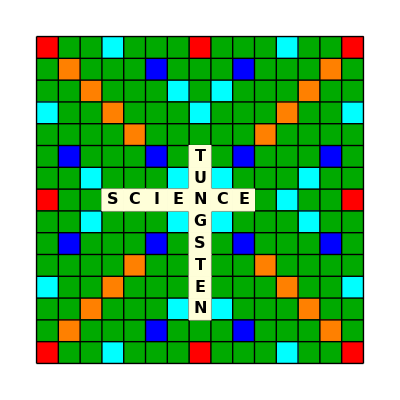

```mathematica
board=CreateInitialScrabbleBoard[];
epilogState=UpdateScrabbleBoard["SCIENCE",{"H",4},"Right",{}];
epilogState=UpdateScrabbleBoard["TUNGSTEN",{"F",8},"Down",epilogState];
Show[board,Epilog->epilogState]
```

I have just picked the position so that the overlap works. How to get around this?

For V1 and V2, we had an association for each game. Now we need an association for each turn.

Rather than making Random Choices, we need to find all possible options and have the user choose.

Some of the logic of how the overlap positions were found.

Defining an overlap vector as position, direction, overlap tile.

Is the problem geometrically solvable? Visualize this with Animate[] and offer it as an exercise to the reader? 98/225

## Plan

Version 3: 1 x 7, 13 x 8 letter words that span the set, with 13 overlaps, and stands as a valid game.
Check that the problem is actually solvable - visualize on board with no letters present.
Visualize the end product. Show an interactive manipulate where the position is chosen.

In real life, 9-letter plays will be more common as the board gets crowded.

Discuss how Wolfram Language made this a breeze.

Discuss why Scrabble should become more popular.

AI Bots are yet to be definitively better than GMs.

Prize money is increasing.

Link to articles about not being a solved game.